## Periodicna motnja

```mathematica
Podatki
```

```mathematica
m=565.0;
k=18800;
d=4500;
F0=2000;
T=6.8;
g=9.81;
ω=2 Pi/T;
Subscript[ω, 0]=√(k/m);
δ= d/(m 2 Subscript[ω, 0]);
```

Sila F1

```mathematica
a0=2/T ∫_0^(T/3) F0ⅆt+2/T  ∫_((2 T)/3)^T 2/3 F0ⅆt;
aj=2/T ∫_0^(T/3) F0 Cos[j ω t] ⅆt+2/T  ∫_((2 T)/3)^T 2/3 F0 Cos[j ω t]ⅆt;
bj=2/T ∫_0^(T/3) F0 Sin[j ω t]ⅆt+2/T  ∫_((2 T)/3)^T 2/3 F0 Sin[j ω t]ⅆt;
```

```mathematica
F5=a0/2 + ∑_(j=1)^5 aj Cos[j ω t]+∑_(j=1)^5 bj Sin[j ω t];
F10=a0/2 + ∑_(j=1)^10 aj Cos[j ω t]+∑_(j=1)^10 bj Sin[j ω t];
F40=a0/2 + ∑_(j=1)^40 aj Cos[j ω t]+∑_(j=1)^40 bj Sin[j ω t];
F400=a0/2 + ∑_(j=1)^400 aj Cos[j ω t]+∑_(j=1)^400 bj Sin[j ω t];
```

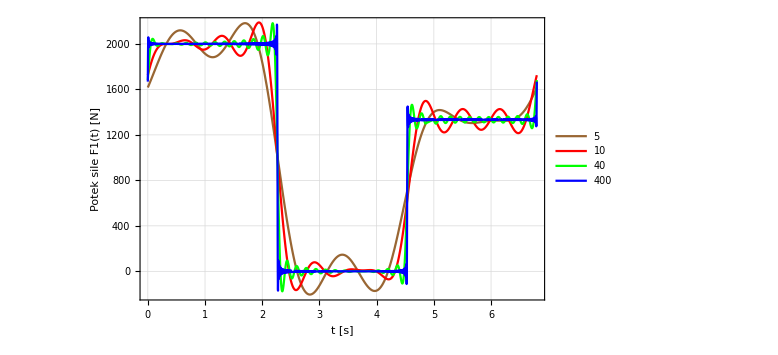

```mathematica
prikaz5=Plot[F5,{t,0,6.8},PlotRange->Full,Frame->True,FrameLabel->{"t [s]","Potek sile F1(t) [N]"},GridLines->Automatic,BaseStyle->{FontFamily->"Courier New",FontSize->10},ImageSize->Large,PlotStyle->Brown,PlotLegends->{"5"}];
prikaz10=Plot[F10,{t,0,6.8},PlotStyle->Red,PlotLegends->{"10"}];
prikaz40=Plot[F40,{t,0,6.8},PlotStyle->Green,PlotLegends->{"40"}];
prikaz400=Plot[F400,{t,0,6.8},PlotStyle->Blue,PlotLegends->{"400"}];
Prikaz=Show[prikaz5,prikaz10,prikaz40,prikaz400]
```

```mathematica
(*Export["Graf_sila1.pdf",Prikaz];
SystemOpen["Graf_sila1.pdf"];*)
```

```mathematica
Izracun odzivov za silo F1!
```

```mathematica
X0=a0/(2 m Subscript[ω, 0]^2);
β=1/(√((1-((j ω)/Subscript[ω, 0])^2)^2+(2 δ  (j ω)/Subscript[ω, 0])^2));
ϕj=ArcTan[1-((ω j)/Subscript[ω, 0])^2,2 δ (j ω)/Subscript[ω, 0]];
xjb=bj/(m Subscript[ω, 0]^2) β Sin[j ω t - ϕj];
xja=aj/(m Subscript[ω, 0]^2) β Cos[j ω t - ϕj];
```

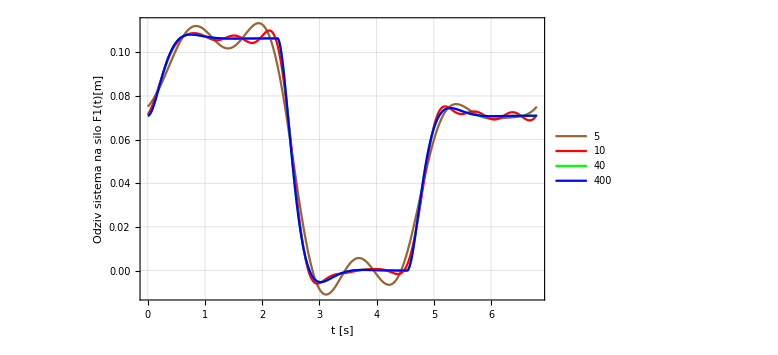

```mathematica
X5=X0+∑_(j=1)^5 xja+∑_(j=1)^5 xjb;
X10=X0+∑_(j=1)^10 xja+∑_(j=1)^10 xjb;
X40=X0+∑_(j=1)^40 xja+∑_(j=1)^40 xjb;
X400=X0+∑_(j=1)^400 xja+∑_(j=1)^400 xjb;
prikazX5=Plot[X5,{t,0,6.8 1},PlotRange->Full,Frame->True,FrameLabel->{"t [s]","Odziv sistema na silo F1(t)[m]"},GridLines->Automatic,BaseStyle->{FontFamily->"Courier New",FontSize->10},ImageSize->Large,PlotStyle->Brown,PlotLegends->{"5"}];
prikazX10=Plot[X10,{t,0,6.8 1},PlotStyle->Red,PlotLegends->{"10"}];
prikazX40=Plot[X40,{t,0,6.8 1},PlotStyle->Green,PlotLegends->{"40"}];
prikazX400=Plot[X400,{t,0,6.8 1},PlotStyle->Blue,PlotLegends->{"400"}];
Skupen1=Plot[X400,{t,0,6.8 1},PlotRange->{{0,T},{-0.02,0.15}},Frame->True,FrameLabel->{"t [s]","Odziv sistema na obe sili[m]"},GridLines->Automatic,BaseStyle->{FontFamily->"Courier New",FontSize->10},ImageSize->Large,PlotStyle->Blue,PlotLegends->{"Odziv na silo F1(t)"}];
Prikaz=Show[prikazX5,prikazX10,prikazX40,prikazX400]
```

```mathematica
(*Export["Graf_odziv1.pdf",Prikaz];
SystemOpen["Graf_odziv1.pdf"];*)
```

+-+-+-+-+-+-+-+-+-+-+-+-+-+-+-+-+-+-+-+-+-+-+-+-+-+-+
Sila F2

```mathematica
F2=12 F0 Sin[0.2 Pi t] ⅇ^(-2 t);    (*tukaj sta definirani sili*)
F2u=UnitStep[t-(2 T)/3] 8 F0 Sin[0.2 Pi (t-(2 T)/3)] ⅇ^(-2 (t-(2 T)/3));
```

```mathematica
a0=2/T ∫_0^(T/3) F2ⅆt+2/T  ∫_((2 T)/3)^T F2uⅆt;
aj=2/T ∫_0^(T/3) F2 Cos[j ω t] ⅆt+2/T  ∫_((2 T)/3)^T F2u Cos[j ω t]ⅆt;
bj=2/T ∫_0^(T/3) F2 Sin[j ω t]ⅆt+2/T  ∫_((2 T)/3)^T F2u Sin[j ω t]ⅆt;
```

```mathematica
F5=a0/2 + ∑_(j=1)^5 aj Cos[j ω t]+∑_(j=1)^5 bj Sin[j ω t];
F10=a0/2 + ∑_(j=1)^10 aj Cos[j ω t]+∑_(j=1)^10 bj Sin[j ω t];
F40=a0/2 + ∑_(j=1)^40 aj Cos[j ω t]+∑_(j=1)^40 bj Sin[j ω t];
F400=a0/2 + ∑_(j=1)^400 aj Cos[j ω t]+∑_(j=1)^400 bj Sin[j ω t];
```

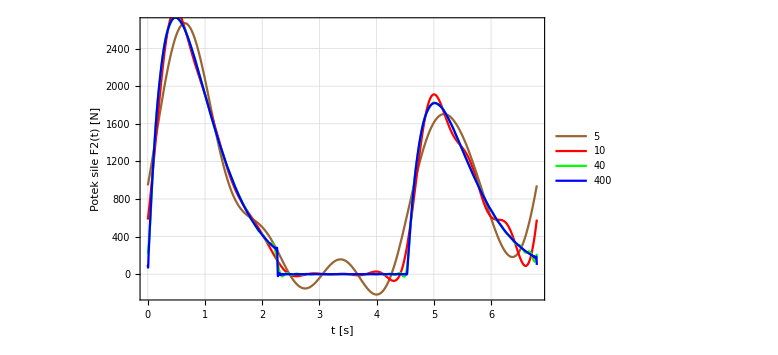

```mathematica
prikaz5=Plot[F5,{t,0,6.8},PlotRange->Full,Frame->True,FrameLabel->{"t [s]","Potek sile F2(t) [N]"},GridLines->Automatic,BaseStyle->{FontFamily->"Courier New",FontSize->10},ImageSize->Large,PlotStyle->Brown,PlotLegends->{"5"}];
prikaz10=Plot[F10,{t,0,6.8},PlotStyle->Red,PlotLegends->{"10"}];
prikaz40=Plot[F40,{t,0,6.8},PlotStyle->Green,PlotLegends->{"40"}];
prikaz400=Plot[F400,{t,0,6.8},PlotStyle->Blue,PlotLegends->{"400"}];
Prikaz=Show[prikaz5,prikaz10,prikaz40,prikaz400]
```

```mathematica
(*Export["Graf_sila2.pdf",Prikaz];
SystemOpen["Graf_sila2.pdf"];*)
```

```mathematica
Izracun odzivov za silo F2!
```

```mathematica
X0=a0/(2 m Subscript[ω, 0]^2);
β=1/(√((1-((j ω)/Subscript[ω, 0])^2)^2+(2 δ  (j ω)/Subscript[ω, 0])^2));
ϕj=ArcTan[1-((ω j)/Subscript[ω, 0])^2,2 δ (j ω)/Subscript[ω, 0]];
xjb=bj/(m Subscript[ω, 0]^2) β Sin[j ω t - ϕj];
xja=aj/(m Subscript[ω, 0]^2) β Cos[j ω t - ϕj];
```

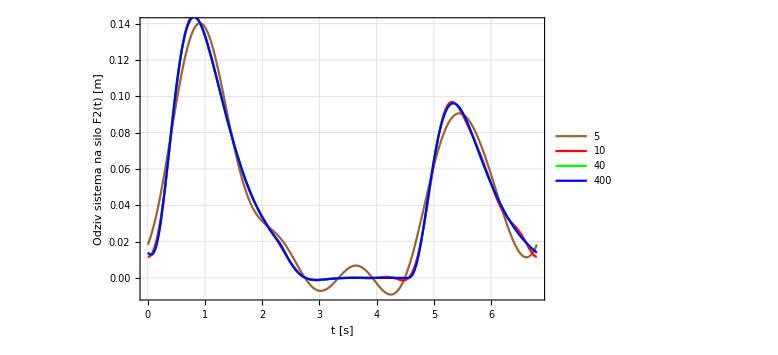

```mathematica
X5=X0+∑_(j=1)^5 xja+∑_(j=1)^5 xjb;
X10=X0+∑_(j=1)^10 xja+∑_(j=1)^10 xjb;
X40=X0+∑_(j=1)^40 xja+∑_(j=1)^40 xjb;
X400=X0+∑_(j=1)^400 xja+∑_(j=1)^400 xjb;
prikazX5=Plot[X5,{t,0,6.8 1},PlotRange->Full,Frame->True,FrameLabel->{"t [s]","Odziv sistema na silo F2(t) [m]"},GridLines->Automatic,BaseStyle->{FontFamily->"Courier New",FontSize->10},ImageSize->Large,PlotStyle->Brown,PlotLegends->{"5"}];
prikazX10=Plot[X10,{t,0,6.8 1},PlotStyle->Red,PlotLegends->{"10"}];
prikazX40=Plot[X40,{t,0,6.8 1},PlotStyle->Green,PlotLegends->{"40"}];
prikazX400=Plot[X400,{t,0,6.8 1},PlotStyle->Blue,PlotLegends->{"400"}];
Skupen2=Plot[X400,{t,0,6.8 1}, PlotStyle->Red,PlotLegends->{"Odziv na silo F2(t)"}];
Prikaz=Show[prikazX5,prikazX10,prikazX40,prikazX400]
```

```mathematica
(*Export["Graf_odziv2.pdf",Prikaz];
SystemOpen["Graf_odziv2.pdf"];*)
```

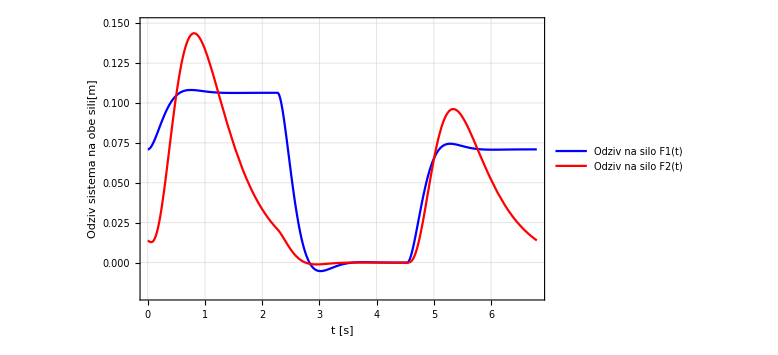

```mathematica
Prikaz=Show[Skupen1, Skupen2]
```

```mathematica
(*Export["Graf_odzivskupen.pdf",Prikaz];
SystemOpen["Graf_odzivskupen.pdf"];*)
```